```mathematica
(** This notebook plots energy eigenvalues of higher order topological insulator (HOTI) phases, more specifically second order topological insulators (SOTI) **)
```

```mathematica
datFileEnergylocation="/HOTI/energies/";
datfileOBCName="t0=1.0_t=1.0_m_0=-1.0_Delta=1.0_x_periodic=0_y_periodic=0_L=60_m=0.6180339887498949_c1=-2_c2=4.5";
```

```mathematica
StringJoin[datFileEnergylocation,datfileOBCName]
```

/HOTI/energies/t0=1.0_t=1.0_m_0=-1.0_Delta=1.0_x_periodic=0_y_periodic=0_L=60_m=0.6180339887498949_c1=-2_c2=4.5

```mathematica
Clear[dataEnergyOBC]
```

```mathematica
(** Change the filenames accordingly and import the dat files **)
```

```mathematica
dataEnergyOBC=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,".csv"]]];
```

```mathematica
Clear[Lattice];
```

```mathematica
Lattice=Table[{j,0},{j,1,Dimensions[dataEnergyOBC][[1]]/4}];
```

```mathematica
largestX = Dimensions[Lattice][[1]]
```

386

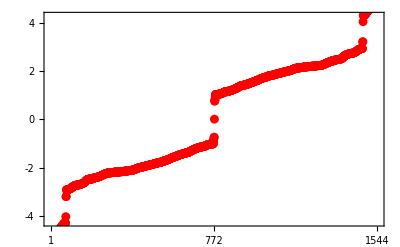

```mathematica
plt1=Show[
ListPlot[dataEnergyOBC,Frame-> True,Axes-> False,PlotRange-> {{0,4*largestX},{-4.25,4.25}},PlotStyle-> {Red,PointSize[0.016]},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-4,-2,0,2,4},None},{{1,2*largestX,4*largestX},None}},BaseStyle-> 18]

(**Plot[3,{x,largestX-350,largestX-550},PlotStyle-> {Thick,Red}],
Plot[1.5,{x,largestX-350,largestX-550},PlotStyle-> {Thick,Black}],

Epilog-> {Inset["OBC",{largestX,3}],Inset["PBC",{largestX,1.5}]}**)
]
```

```mathematica
largestX
```

386

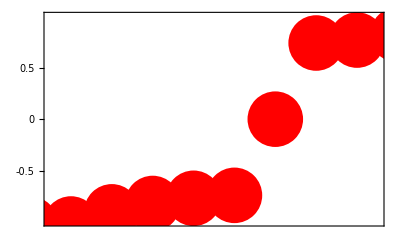

```mathematica
plt2=Show[
ListPlot[dataEnergyOBC,Frame-> True,Axes-> False,PlotRange-> {{2*largestX-3.5,2*largestX+4.5},{-1,1}},PlotStyle-> {Red,PointSize[0.1]},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-0.5,0,0.5},None},{None,None}},BaseStyle-> 36]

(**Plot[3,{x,largestX-350,largestX-550},PlotStyle-> {Thick,Red}],
Plot[1.5,{x,largestX-350,largestX-550},PlotStyle-> {Thick,Black}],

Epilog-> {Inset["OBC",{largestX,3}],Inset["PBC",{largestX,1.5}]}**)
]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,".pdf"],plt1];
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,"zoom.pdf"],plt2];
```